```mathematica
hourlyBostonTemperatureTimeSeriesHasMissing=TimeSeriesResample[WeatherData["KBOS","Temperature",{{2012,9,1},{2019,6,31}}],"Hour"]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
RegularlySampledQ[%]
```

True

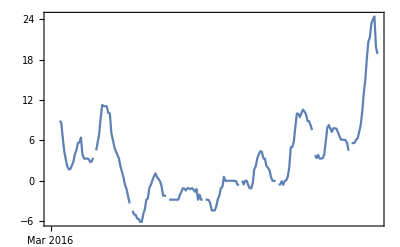

toAssociation⟦{{Sat 1 Sep 2012 00:00:00GMT-4.,28.3},{Sat 1 Sep 2012 01:00:00GMT-4.,27.15},{Sat 1 Sep 2012 02:00:00GMT-4.,26.64},{Sat 1 Sep 2012 03:00:00GMT-4.,26.1},{Sat 1 Sep 2012 04:00:00GMT-4.,26.7},{Sat 1 Sep 2012 05:00:00GMT-4.,26.1+0.981818 (-26.1+Missing[NotAvailable])},59868,{Mon 1 Jul 2019 18:00:00GMT-4.,23.3},{Mon 1 Jul 2019 19:00:00GMT-4.,24.46},{Mon 1 Jul 2019 20:00:00GMT-4.,25.11},{Mon 1 Jul 2019 21:00:00GMT-4.,26.1},{Mon 1 Jul 2019 22:00:00GMT-4.,26.16},{Mon 1 Jul 2019 23:00:00GMT-4.,26.86}}⟧
 |  |  |  |

```mathematica
DateListPlot[TimeSeriesWindow[hourlyBostonTemperatureTimeSeriesHasMissing,{DateObject[{2016,3,1}],DateObject[{2016,3,9}]}]]
```

```mathematica
SynthesizeMissingValues[Dataset@AssociationThread[hourlyBostonTemperatureTimeSeriesHasMissing["Dates"]->hourlyBostonTemperatureTimeSeriesHasMissing["Values"]]]
```

SynthesizeMissingValues::mlinclgth: Incompatible lengths: all features should contain the same number of examples.

SynthesizeMissingValues[Dataset[<>]]

```mathematica
18.9+0.9818181818181818 (-18.9+Missing["NotAvailable"])
```